```mathematica
C
```

{A→5.94081,B→-0.171391}

```mathematica
NSolve[0== 7/2*R*Log[T/693]-R*Log[1/8],T]
```

{{T→382.567}}

```mathematica
NSolve[7/2*0.008314*(T-673.15)== -5.0734048302,T]
```

{{T→498.8}}

```mathematica
A=9.353
B=2696.79
Ci=-46.16

NSolve[Log[1.013]== A-B/(T+Ci)]
```

9.353

2696.79

-46.16

{{T→334.893}}

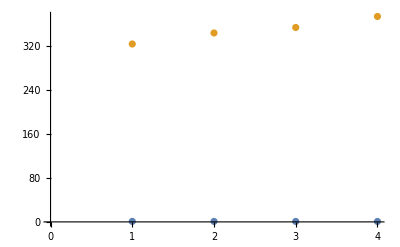

```mathematica
ListPlot[{{0.941,0.870,0.846,0.808},{323.2,343.2,353.2,373.2}}]
```

```mathematica
Log[{0.941,0.870,0.846,0.808}]

Fit[Log[{0.941,0.870,0.846,0.808}],{1,T^-1},T]
```

{-0.0608121,-0.139262,-0.167236,-0.213193}

-0.241832+0.185675/T

```mathematica
data= {{323.2,-0.060812139396757475},{343.2,-0.13926206733350766},{353.2,-0.1672359193759138},{373.2,-0.2131932204610416}}
```

{{323.2,-0.0608121},{343.2,-0.139262},{353.2,-0.167236},{373.2,-0.213193}}

```mathematica
line=Fit[data,{1,T^-1},T]
```

-1.20561+368.27/T

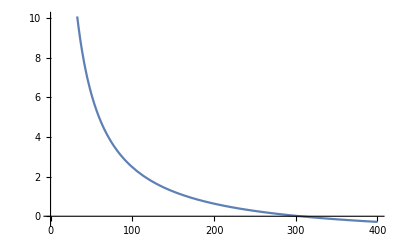

```mathematica
Plot[-1.2056143474837067+368.27000271328694/T,{T,0,400}]
```

```mathematica
h[T_]:=-1.2056143474837067+368.27000271328694/T
16.3*575.4*Exp[h[298.15]]
```

9660.49

```mathematica
Solve[23.23*1.013== (1-x2)*0.0314+(x2)698.9*x2,x2]
```

{{x2→-0.183349},{x2→0.183394}}

```mathematica
((1.483*10^-3)*(23.23))/0.03126
```

1.10205

```mathematica
Clear[x1,x2,P]
x1=1-x2
P1=79.80
P2=40.50

γ1=Exp[0.95*x2^2]
γ2=Exp[0.95*x1^2]
y1=0.05
y2=0.95
P*(y1/(γ1*P1)+y2/(γ2*P2))== 1

Solve[P*(y1/(γ1*P1)+y2/(γ2*P2))== 1,P]
```

1-x2

79.8

40.5

ⅇ^(0.95 x2^2)

ⅇ^(0.95 (1-x2)^2)

0.05

0.95

(0.0234568 ⅇ^(-0.95 (1-x2)^2)+0.000626566 ⅇ^(-0.95 x2^2)) P==1

{{P→1./(0.0234568 ⅇ^(-0.95 (1.-1. x2)^2)+0.000626566 ⅇ^(-0.95 x2^2))}}

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of ⅇ^(-0.95 (1-x2)^2).

Hold[x=y2/(γ2 P2)]

```mathematica
Manipulate[List[1./(0.023456790123456788 ⅇ^(-0.95 (1.-1. x2)^2)+0.0006265664160401003 ⅇ^(-0.95 x2^2)),(Exp[0.95*(1-x2)^2]*40.50*x2)/y2],{x2,0,4}]
```

```mathematica
FindRoot[1./(0.023456790123456788 ⅇ^(-0.95 (1.-1. x2)^2)+0.0006265664160401003 ⅇ^(-0.95 x2^2))== (Exp[0.95*(1-x2)^2]*40.50*x2)/y2,{x2,1}]
```

{x2→0.989573}